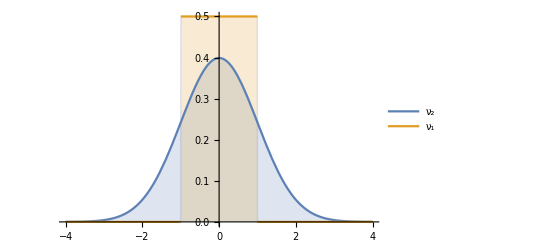

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],
PDF[UniformDistribution[{-1,1}],x]}//Evaluate, {x, -4,4},Filling->Axis, PlotLegends->Placed[{Subscript[ν, 2],Subscript[ν, 1]},{0.9,0.7}]]
```

```mathematica
f[x_]:=CDF[NormalDistribution[0,1],x];
g[y_]:=CDF[UniformDistribution[{-1,1}],y];
Plot3D[{f[x]+g[y] - Abs[f[x]-g[y]]}/2
//Evaluate, {x, -3,3}, {y, -2,2}, AxesLabel->{Subscript[ν, 2],Subscript[ν, 1]},LabelStyle->Directive[Blue,Bold]]
```

-Graphics3D-